```mathematica
ClearAll["Global+`*"];(*Plot[{Subscript[N, 0],value[[1]]/.plots,value[[2]]/.plots,value[[3]]/.plots},{t,0,T},PlotStyle->{{Green,Dashed},Orange,Red,Gray},PlotLegends->Placed[{"N_0","X(t)","Y(t)","Z(t)"},Above],AxesLabel->{"t","X,Y,Z"}]*)
```

```mathematica
data1=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 1\\program\\Проект1\\Проект1\\iter.txt","Data"];
```

```mathematica
data2=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 1\\program\\Проект1\\Проект1\\iter.txt","Data"];
```

```mathematica
data3=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 1\\program\\Проект1\\Проект1\\iter.txt","Data"];
```

```mathematica
data4=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 1\\program\\Проект1\\Проект1\\iter.txt","Data"];
```

```mathematica
data5=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 1\\program\\Проект1\\Проект1\\iter.txt","Data"];
```

```mathematica
data6=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 1\\program\\Проект1\\Проект1\\iter.txt","Data"];
```

```mathematica
data7=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 1\\program\\Проект1\\Проект1\\iter.txt","Data"];
```

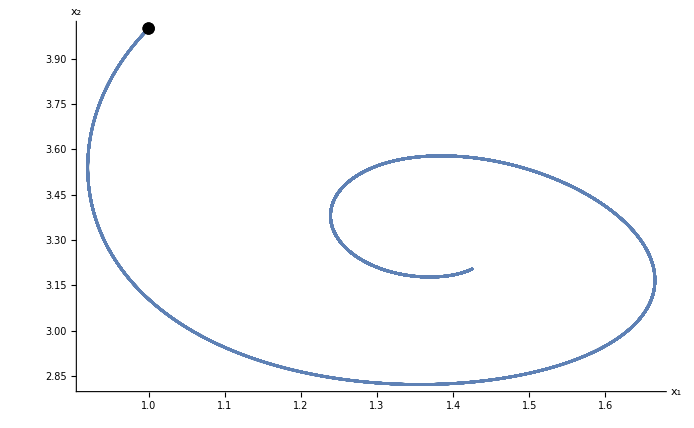

```mathematica
Show[ListPlot[{data1(*,data2,data3,data4,data5,data6,data7*)},AxesLabel->{"x_1","x_2"},AxesStyle->Thick,LabelStyle->Directive[20]],ListPlot[{data1⟦1⟧},PlotStyle->Black]]
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
data=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 1\\program\\Проект1\\Проект1\\iter.txt","Data"];ListPointPlot3D[data,AxesLabel->{"x","y","z"},AxesStyle->Thick,LabelStyle->Directive[20]]
```

-Graphics3D-